# Generating Trajectories of BZ Life Forms (Chemits)

#### Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
baseDirectory=NotebookDirectory[]
```

\\SCAPA4\scapa4\group\0-Papers in Progress\BZ_CA_Computation_Abhishek_Marcus\current working documents\data\Mathematica_Notebooks\Sim_InitPopulations_Long\

## Creating Snapshots from the simulation for Video

```mathematica
runID=10;nSteps=15000;
```

```mathematica
allPWMStates1=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[1]<>".mx"];
allPWMStates10=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[10]<>".mx"];allPWMStates100=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[100]<>".mx"];allPWMStates1000=Import[baseDirectory<>"PWM_data"<>ToString[runID]<>"_"<>ToString[1000]<>".mx"];
```

```mathematica
plotCells[timeStep_]:=Panel[GraphicsGrid[Partition[{MatrixPlot[allPWMStates1⟦timeStep⟧,PlotLabel-> "Initial Life Forms 1",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}],MatrixPlot[allPWMStates10⟦timeStep⟧,PlotLabel-> "Initial Life Forms 10",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}],MatrixPlot[allPWMStates100⟦timeStep⟧,PlotLabel-> "Initial Life Forms 100",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}],MatrixPlot[allPWMStates1000⟦timeStep⟧,PlotLabel-> "Initial Life Forms 1000",ImageSize->300,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},ColorRules->{1->White,2-> Orange,3-> Red,4->Blue}]},2],Spacings-> {0,10},Frame-> All],Style["Time Step: "<>ToString[timeStep],16],{{Top,Center}}]
```

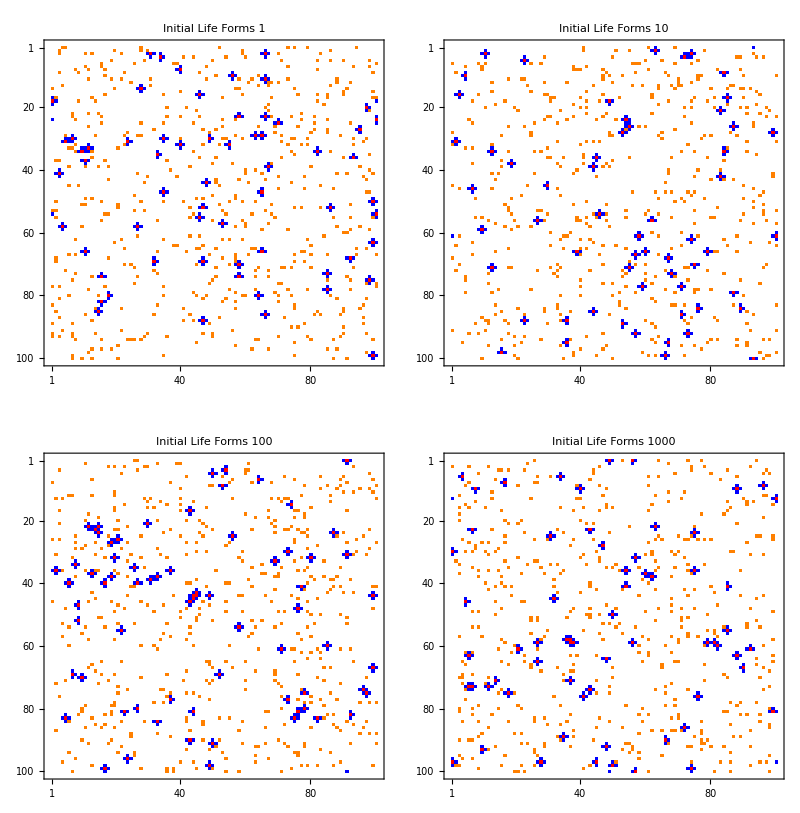
-Graphics-Time Step: 15000

```mathematica
plotCells[15000]
```

```mathematica
SetDirectory[baseDirectory<>"Images\\"]
```

D:\Projects\BZ2\Sim_InitPopulations_Long\Images

```mathematica
Parallelize[Map[Export["Image_"<>ToString[#]<>".png",plotCells[#]]&,Range[nSteps]]];
```